```mathematica
ReIm={Re[#],Im[#]}&;
EToIPi[j_]:=(E)^(I*j);
ListPlotIm = ListPlot[ReIm/@#,AspectRatio->1,PlotRange->{{-1.2,1.2},{-1.2,1.2}}]&;
Manipulate[
p2=ParametricPlot[ReIm[EToIPi[k]],{k,0,Pi}];
p1=ListPlot[
{ReIm[EToIPi[x]],{Cos[Log[3]],Sin[Log[3]]}},
AspectRatio->1,
PlotRange->{{-1.1,1.1},{-1.1,1.1}}
];
Show[p1,p2]
,{x,0,2Pi}]
```

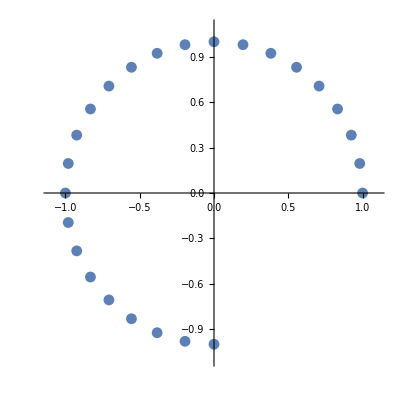

```mathematica
ListPlotIm[(E^#)&/@Range[0I,(3/2)*Pi*I, (Pi/16)I]]
```

```mathematica
F [x_]:=(E)^x;
Manipulate[Column[{i, F[i], ListPlotIm[{F[i]}]}],{i,0,4Pi*I}]
```